```mathematica
f=(Log[Log[x]]+2Tan[x])/(Log[y]-1)
g=D[f,y]
```

(Log[Log[x]]+2 Tan[x])/(-1+Log[y])

-(Log[Log[x]]+2 Tan[x])/(y (-1+Log[y])^2)

```mathematica
Plot3D[{f,g},{x,0,5},{y,0,5}]
```

-Graphics3D-

```mathematica
A={{1,1},{1,2}}
```

{{1,1},{1,2}}

```mathematica
char=CharacteristicPolynomial[A,x]
```

1-3 x+x^2

```mathematica
vals=Solve[char==0,x]
```

{{x→1/2 (3-√5)},{x→1/2 (3+√5)}}

```mathematica
eigs=Eigenvalues[A]
```

{1/2 (3+√5),1/2 (3-√5)}

```mathematica
vecs={{1,1},{0,1},{1,0},{0,0},{1/2,1/2}}
```

{{1,1},{0,1},{1,0},{0,0},{1/2,1/2}}

```mathematica
Thread[Times[A,]&,vecs]
```

A Null&

```mathematica
vecsnew=A.vecs[[#]]&/@Range[1,Length[vecs]]
```

{{2,3},{1,2},{1,1},{0,0},{1,3/2}}

```mathematica
pts=Table[Point[{vecs[[n]]}],{n,1,Length[vecs]}];
ptsnew=Table[Point[{vecsnew[[n]]}],{n,1,Length[vecsnew]}];
```

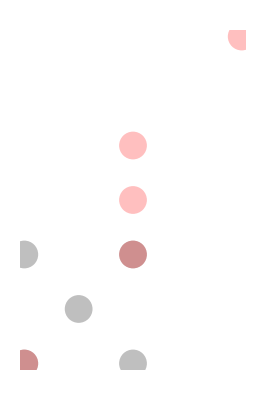

```mathematica
Graphics[{
{Black,Opacity[0.25],PointSize[0.05],pts},
{Red,Opacity[0.25],PointSize[0.05],ptsnew}
}]
```

```mathematica
?Eigenvalues
```

Eigenvalues[m] gives a list of the eigenvalues of the square matrix m. 
Eigenvalues[{m,a}] gives the generalized eigenvalues of m with respect to a. 
Eigenvalues[m,k] gives the first k eigenvalues of m. 
Eigenvalues[{m,a},k] gives the first k generalized eigenvalues.

```mathematica
eigs
```

{1/2 (3+√5),1/2 (3-√5)}

```mathematica
eigs[[1]]>1
eigs[[2]]<1
eigs[[1]]==1/eigs[[2]]
```

True

True

True

```mathematica
GoldenRatio^2//N
N[eigs[[1]]]
```

2.61803

2.61803

```mathematica
eigvecs=Eigenvectors[A]
```

{{1/2 (-1+√5),1},{1/2 (-1-√5),1}}

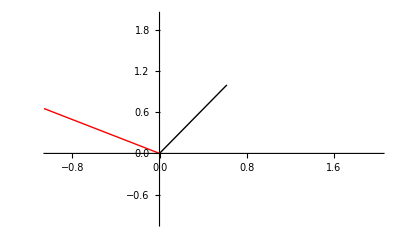

```mathematica
Show[{
Plot[0,{x,-1,2},PlotRange->{-1,2},PlotStyle->Opacity[0],Ticks->None],
Graphics[{
{Line[{{0,0},eigvecs[[1]]}]},
{Red,Line[{{0,0},eigvecs[[2]]}]}
}]
}]
```

```mathematica
Graphics[{
{Black,Opacity[0.25],PointSize[0.05],pts},
{Red,Opacity[0.25],PointSize[0.05],ptsnew}
}]
```

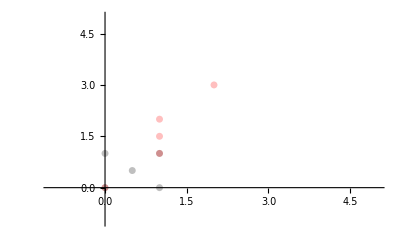

```mathematica
Show[{
Plot[0,{x,-1,5},PlotRange->{-1,5},PlotStyle->Opacity[0],Ticks->None],
Graphics[{
{Black,Opacity[0.25],PointSize[0.0125],pts},
{Red,Opacity[0.25],PointSize[0.0125],ptsnew}
}]
}]
```